# Diameter

### Author

Eric W. Weisstein
August 19, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneGeometry/Diameter.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Diameter.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Figure

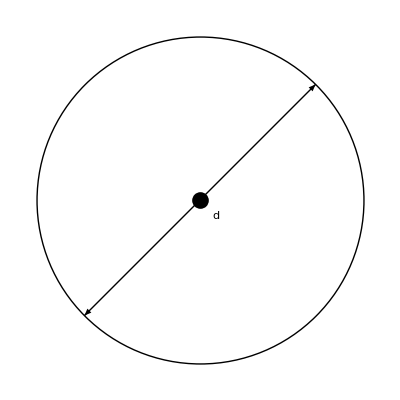

```mathematica
circle=Graphics[{
Circle[{0,0},1],
Arrowheads[{-1,1}.07],Arrow[{-{1,1},{1,1}}/√2],
PointSize[.03],Point[{0,0}],
Text[Style["d",Italic],.1{1,-1}]
},PlotRangePadding->.5]
```

```mathematica
sphere=Show[{
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2π},{v,0,π},Boxed->False,Axes->False,PlotStyle->None,MeshStyle->GrayLevel[.5]],
Graphics3D[{PointSize[.03],Point[{0,0,0}],Arrowheads[{-1,1}.05],Arrow[.585{{-1,-1,-1},{1,1,1}}],Text[Style["d",Italic],.15{1,0,-1},Background->White]}]
}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{circle,sphere}},Spacings->-100,Alignment->Center]
```

-Graphics-